```mathematica
Module[{c1,c2,c3},
c1={{0,0},{1,1}};
c2=Reverse@{{0,1},{1,2}};
c3={{0,0.5},{1,1.5}};

Graphics[{
Thick,Line@c1,Line@c2,
Opacity[0.5,Pink],FilledCurve[{Line@c1,Line@c2}],
Blue,(*Point@RandomPoint[FilledCurve[{Line@c1,Line@c2}],100]*)
Point@RandomPoint[{Thickness@0.65,Line@c3},100]
}]
]
```

RandomPoint::creg: The first argument {Thickness[0.65],Line[{{0,0.5},{1,1.5}}]} is expected to be a parameter-free region.

-Graphics-

```mathematica
Module[{c1,c2},
c1={{0,0},{1,1}};
c2=Reverse@{{0,1},{1,2}};
```

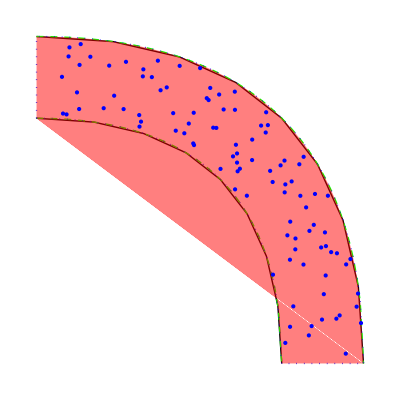

```mathematica
Module[{c1,c2,f1,f2,g1,g2,h1,h2},
c1={{0,0},{1,0},{1,-1}};
c2={{0,-0.25},{0.75,-0.25},{0.75,-1}};

f1=Quiet@Interpolation[BezierFunction[c1][#]&/@Range[0,1,0.01]];
g1={#,f1[#]}&/@Range[0,1,0.01];
h1=Join[{{0,-0.25}},g1];

f2=Quiet@Interpolation[BezierFunction[c2][#]&/@Range[0,1,0.01]];
g2={#,f2[#]}&/@Range[0,0.75,0.01];
h2=Join[g2,{{1,-1}}];

Graphics@{Thick,
BezierCurve@c1,BezierCurve@c2,
Green,Dashed,Line@g1,Line@g2,
Blue,Dotted,Line@h1,Line@h2,
EdgeForm@None,(*{Red,Dotted},*)FaceForm@Opacity[0.5,Red],Polygon[Join[h2,h1]],
Point@RandomPoint[Polygon[Join[h2,h1]],100]
}
]
```

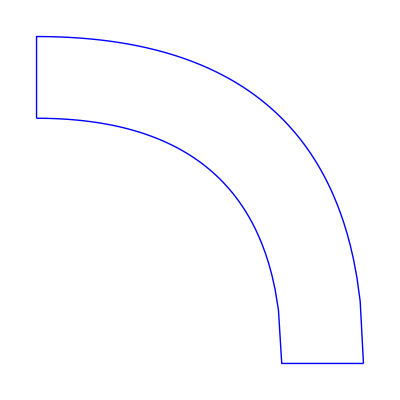

```mathematica
Module[{c1,c2,f1,f2,g1,g2,h1,h2,j1,j2,k1,k2},
c1={{0,0},{1,0},{1,-1}};
c2={{0,-0.25},{0.75,-0.25},{0.75,-1}};

f1=Quiet@Interpolation[BezierFunction[c1][#]&/@Range[0,1,0.01]];
g1={#,f1[#]}&/@Range[0,1,0.01];
h1=Join[{{0,-0.25}},g1];

f2=Quiet@Interpolation[BezierFunction[c2][#]&/@Range[0,1,0.01]];
g2={#,f2[#]}&/@Range[0,0.75,0.01];
h2=Join[g2,{{1,-1}}];

j1=Quiet@Interpolation[h1];j2=Quiet@Interpolation[h2];
k1=Quiet@Interpolation[Map[Reverse,h1],InterpolationOrder->1];
k2=Quiet@Interpolation[Map[Reverse,h2],InterpolationOrder->1];

Graphics@{Thick,
Blue,Line@h1,Line@h2,
Table[Point
}
]
```

```mathematica
Module[{w,l,h,m,building,side,getInsidePolyTest,inBuildingQ,pts},
w=100;l=200;h=30;m=70;

building={
{{0,l,0},{w,l,0},{w,l,h},{0,l,h}},
{{0,0,0},{0,0,h},{0,l,h},{0,l,0}},
{{w,0,0},{w,0,h},{w,l,h},{w,l,0}},
{{0,0,0},{w,0,0},{w,l,0},{0,l,0}},
{{0,0,0},{w,0,0},{w,0,h},{0,0,h}},
{{0,0,h},{w/2,0,m},{w/2,l,m},{0,l,h}},
{{w,0,h},{w/2,0,m},{w/2,l,m},{w,l,h}},
{{w,l,h},{w/2,l,m},{0,l,h}},
{{w,0,h},{w/2,0,m},{0,0,h}}
};

side[{P_,Q_,R_,___},X_]:=Det@Differences[{X,P,Q,R}];

getInsidePolyTest[poly_,knownPointInside_]:=Module[{known=Positive[side[#,knownPointInside]&/@poly]},Function[pt,(known==Positive[side[#,pt]&/@poly])]];
inBuildingQ=getInsidePolyTest[building,{1,1,1}];

pts=Select[RandomVariate[UniformDistribution[{{0,w},{0,l},{0,m}}],1000],inBuildingQ];

Graphics3D[{FaceForm[Opacity[0.2]],Polygon@building,Point[pts]}];getInsidePolyTest[
]
```

{{10.8699,162.147,34.7848},{39.5019,180.608,57.3939},{39.8636,21.3976,31.8215},{24.391,21.1254,17.7751},{44.5321,43.1324,3.36187},{27.7559,10.8464,18.3244},{5.48268,102.025,31.3795},{64.5089,107.466,14.1494},{14.9849,52.3404,9.76024},{34.1353,199.149,40.2636},{49.5669,132.493,19.3829},{60.961,69.9994,26.2532},{40.9174,69.5536,4.26849},{92.8761,122.66,7.77727},{55.47,166.696,18.954},{29.6783,13.4795,5.51418},{62.357,27.8278,5.42748},{74.3697,189.802,47.7523},{68.0488,39.9652,40.5592},{43.6008,45.0402,48.8022},{86.5972,181.457,36.8029},{86.8766,180.438,21.4435},{49.7193,46.3184,37.0932},{20.4919,134.644,24.7288},{75.5042,138.741,7.61305},{94.5213,135.048,33.1739},{56.5881,64.6717,31.3608},{26.41,99.2997,17.0509},{52.0458,24.527,55.5037},{30.9958,183.512,17.1806},{0.593714,30.5702,15.6127},{55.0552,93.6126,12.9757},{78.3293,164.694,14.0779},{12.5632,18.2946,34.2634},{22.3451,101.497,40.6276},{51.7511,33.6184,16.2841},{86.5414,68.1202,18.2626},{7.67091,152.968,27.6295},{81.6829,174.01,22.6604},{33.9084,189.271,12.5235},{60.4718,133.165,48.1579},{61.3039,96.0432,53.4292},{49.8842,118.885,8.23069},{50.3837,99.6179,68.2182},{39.8969,110.255,57.9211},{85.5055,45.7171,34.5609},{5.60427,174.039,16.7853},{17.4837,91.7973,29.9208},{31.7143,97.0371,30.2093},{28.2219,32.4912,10.0813},{77.8167,153.286,30.3996},{41.2871,77.2256,57.561},{40.8543,26.6498,18.7044},{20.4133,37.8044,41.9156},{53.8239,61.9867,47.3843},{90.9077,51.5997,16.4432},{18.3952,156.461,28.8766},{10.8243,62.9427,17.8384},{92.9543,87.6003,35.6305},{64.3888,92.1904,42.6517},{45.6633,149.841,12.1428},{8.26706,93.5083,30.5779},{0.0373482,96.9918,12.0187},{43.0873,192.848,4.98711},{17.8195,28.7657,19.4406},{40.0751,190.823,55.0861},{21.628,60.4722,36.5109},{77.1707,177.749,4.61871},{23.3043,88.8402,37.3144},{59.101,8.42169,57.2621},{69.9608,193.352,53.4589},{44.5736,133.591,10.5675},{51.1054,189.172,65.2323},{1.27951,107.494,26.5845},{25.559,94.6006,17.3056},{43.0161,65.8439,34.4989},{41.964,101.048,29.4625},{53.5257,17.734,55.2301},{1.80259,90.9192,29.8253},{12.6903,21.9813,33.4003},{77.7432,4.35617,29.5415},{79.462,105.039,9.26482},{47.7419,174.656,64.4415},{70.4117,155.057,5.68635},{24.3817,15.8611,36.6465},{13.4376,98.7189,27.8316},{26.6862,163.693,51.1091},{3.81538,149.697,22.7252},{56.0945,90.5335,63.5478},{12.905,51.9213,6.69344},{76.3772,145.53,7.27212},{62.7589,158.209,46.6618},{1.43349,45.4988,7.28308},{58.3261,192.771,25.1057},{45.364,81.626,2.36523},{24.0986,104.758,32.3387},{38.6701,92.158,36.5856},{66.3442,23.2574,13.7229},{12.074,10.8883,26.6286},{80.4574,98.6822,27.1484},{54.7073,157.347,6.67258},{52.572,85.43,5.97596},{78.5372,16.4587,41.5145},{44.3235,84.6218,3.26507},{73.0836,0.0598794,1.608},{90.0388,152.731,18.3161},{94.9819,44.388,6.26202},{50.5758,198.037,19.4298},{10.0556,89.4929,36.7443},{18.8489,90.1477,26.0034},{46.2355,31.8886,27.2889},{81.2976,176.513,22.4281},{84.2471,197.457,25.9005},{67.8629,120.876,10.8836},{42.1979,92.4993,58.2673},{38.7559,96.2415,15.9348},{36.0939,113.031,52.743},{72.9416,49.2111,13.771},{3.40436,165.623,24.5313},{82.6153,120.673,6.99265},{66.2622,103.894,0.879539},{55.831,125.323,47.073},{26.8514,122.085,41.565},{53.2933,26.7719,21.9065},{88.2196,46.3268,29.304},{33.0189,98.7786,51.3663},{79.6885,81.9733,26.0112},{99.8712,33.6482,15.4246},{29.6254,190.705,52.5416},{53.3563,60.7228,21.5698},{91.3588,37.5906,27.1943},{67.1902,156.081,45.312},{76.5356,13.7434,44.7517},{83.3387,101.011,11.651},{74.8038,120.447,47.4548},{76.0151,143.084,27.3892},{62.7631,5.57277,18.6383},{61.7446,53.546,40.7942},{49.1191,71.6597,46.0407},{51.1469,60.8121,38.99},{40.0871,162.174,46.3846},{91.9085,113.515,29.6793},{23.6765,162.909,22.8634},{50.1829,138.918,45.0338},{50.0681,9.23571,46.5564},{82.1573,166.217,22.7129},{47.1737,167.152,53.9719},{43.1685,151.395,37.05},{24.5067,56.4212,11.7458},{1.11668,36.6567,14.2299},{85.8904,163.96,39.8059},{68.1553,132.678,44.6942},{23.7317,186.193,30.1237},{72.1374,195.546,14.0553},{58.5605,128.025,45.2707},{69.3888,89.7984,4.26399},{83.1247,103.12,21.8822},{33.2155,95.9419,23.8071},{97.6976,113.083,22.2186},{59.6402,11.2702,17.4682},{53.0474,73.5572,25.8636},{86.1528,25.2682,2.00904},{4.60256,88.1127,26.4515},{7.29855,138.767,5.10004},{29.0667,51.9194,27.2168},{92.9296,4.13586,7.31823},{44.7806,157.726,50.9296},{37.8867,104.365,9.2322},{38.273,28.9743,32.9626},{8.13489,192.376,3.32507},{57.9311,134.984,36.5275},{53.5591,153.878,59.502},{32.3491,62.9178,16.246},{82.3843,151.035,30.8064},{10.7117,37.0233,10.5929},{69.2783,47.3829,0.908557},{15.536,136.929,20.1692},{63.2252,143.38,28.172},{67.8825,116.401,47.423},{90.2053,156.56,1.83844},{52.7028,100.232,50.9795},{5.18378,185.979,26.6639},{29.2704,77.7559,1.8804},{11.2354,109.076,16.0944},{68.0766,74.8289,48.3999},{33.0258,90.7458,52.3515},{7.77618,74.1069,27.5337},{5.36961,126.029,28.4249},{43.3309,182.304,61.8149},{2.83685,49.3131,12.9067},{22.9085,173.36,26.0112},{78.8031,66.4662,27.6368},{82.8729,168.032,24.2185},{48.8056,89.6177,27.3447},{29.166,3.55149,51.335},{11.3442,38.6242,10.9969},{45.393,127.758,21.7931},{88.1548,84.1524,33.8595},{33.258,60.4737,11.3925},{49.5901,10.5331,32.0588},{17.3164,175.798,16.7716},{68.6006,118.618,44.8259},{35.5162,127.621,22.3136},{34.3324,131.826,35.3526},{56.624,98.3065,44.1261},{15.7462,159.631,4.86732},{44.9955,131.891,60.3401},{58.735,98.5614,53.1494},{13.7169,172.131,2.50146},{55.3639,147.956,63.3091},{77.9406,167.945,10.6409},{15.938,179.218,34.5315},{54.886,129.682,47.5881},{30.8585,49.9393,49.6627},{14.2132,148.996,26.5585},{13.8527,50.7472,13.022},{92.7471,193.585,31.8328},{24.6722,166.858,36.},{71.6655,27.7421,24.2248},{56.9033,60.728,61.8702},{47.6476,180.012,44.0198},{54.0035,116.123,47.2709},{21.8932,63.7759,19.9688},{68.6773,5.54281,28.3233},{83.978,129.48,7.63073},{47.7568,115.857,66.5974},{93.9877,14.0449,24.3204},{21.3692,62.8602,37.6014},{35.115,182.238,4.61126},{46.8962,147.33,37.3802},{57.4156,26.2929,3.68738},{27.6616,129.317,44.5569},{51.9169,14.7475,9.60931},{96.6213,168.2,11.9992},{40.7316,177.949,51.1377},{0.888011,7.11824,6.78253},{19.7592,147.252,2.2278},{29.6025,99.9136,26.3282},{60.7232,123.428,11.4986},{54.2706,194.839,15.1532},{18.5852,139.265,15.3424},{31.5069,172.925,34.5342},{30.1283,159.675,26.9941},{40.8476,34.1409,49.1747},{25.8516,191.783,28.6133},{93.4135,96.7397,12.8922},{40.2157,195.027,52.8413},{81.9838,148.32,38.8383},{35.53,108.2,33.0796},{90.9633,69.0991,27.4716},{35.4497,109.3,11.8259},{25.702,44.7447,48.358},{75.0646,194.002,4.78669},{3.81786,177.833,11.1048},{48.1257,182.303,35.037},{82.0964,135.911,32.237},{79.8537,123.072,22.7521},{11.3956,181.853,1.5972},{8.3959,199.688,21.2587},{65.6267,78.8389,40.8747},{7.18019,125.396,2.25303},{42.4467,126.041,46.587},{40.9467,34.8865,17.1107},{62.3454,53.7841,31.8894},{42.0704,70.4876,57.3003},{18.1646,41.4426,32.1955},{50.0074,80.9199,22.0128},{57.196,40.6018,30.8858},{50.4237,83.9668,54.1159},{18.3803,157.513,21.4186},{26.0446,175.648,19.5969},{21.2118,17.7589,34.1168},{32.6998,159.027,48.0763},{62.4001,85.4561,48.9065},{11.9659,148.198,25.7374},{32.8403,106.003,34.4528},{50.9103,169.641,11.9451},{1.21921,59.9857,9.15804},{11.1986,102.771,1.35048},{11.9772,60.3521,21.6288},{29.2787,53.1401,31.6123},{1.0843,125.716,26.1545},{28.7421,142.475,40.1235},{60.9041,147.473,43.2608},{48.1566,123.529,67.6776},{40.6048,90.0927,34.1255},{29.6543,54.4743,8.95237},{24.338,193.566,30.8503},{73.1978,185.942,32.3501},{28.0584,146.579,46.838},{13.6488,87.4961,32.5408},{84.3871,26.9583,17.2454},{34.5655,53.3019,55.3529},{43.3481,71.7784,45.9139},{50.7841,154.297,21.027},{26.1415,182.879,42.5413},{30.7331,53.7701,6.63337},{47.7488,198.444,43.8625},{44.1296,8.28521,57.0254},{86.0655,79.5825,23.7502},{91.1709,144.241,29.8326},{85.7289,118.794,30.4792},{38.7915,84.9264,26.1637},{60.348,36.1508,32.6452},{22.3196,140.271,5.04119},{16.8016,67.3851,10.595},{65.971,75.8154,43.3979},{97.431,3.47519,0.0997807},{84.1706,169.815,17.5947},{18.2188,52.8789,34.992},{1.71573,73.59,4.06364},{23.1892,92.3039,36.3888},{74.1317,76.5305,16.6962},{23.5072,196.286,36.1056},{41.4315,169.735,28.2318},{2.49156,62.9297,12.1766},{17.931,69.7343,14.7698},{70.2592,2.66256,52.1396},{59.2296,161.006,28.4236},{57.726,122.67,14.9061},{12.3107,110.788,12.8579},{79.6672,64.4749,20.2671},{11.3996,88.1822,5.4692},{7.09061,164.811,12.9028},{77.1041,97.6449,32.668},{41.1367,8.47282,0.748534},{82.3251,165.575,38.2174},{84.0828,85.8116,17.5163},{84.3642,91.4456,11.7345},{63.6354,160.599,2.63222},{25.6141,73.6861,20.0412},{79.8914,133.54,16.3159},{12.9056,121.763,14.0916},{78.039,12.9067,7.81688},{25.7793,82.4481,29.8686},{13.5497,138.518,1.54134},{37.9193,193.684,44.562},{81.5758,106.349,13.0978},{65.1636,4.30317,51.3278},{77.7445,132.018,30.9704},{76.6737,186.638,14.7534},{31.2578,170.728,18.0614},{82.7863,154.131,13.9851},{64.8499,14.2308,14.4945},{62.6252,187.117,47.4416},{37.7119,187.9,59.984},{36.4635,20.4821,2.13733},{64.0014,109.441,35.5255},{18.4762,65.6784,38.0737},{43.9506,108.87,12.7898},{39.6783,9.17171,26.1315},{12.6738,189.958,34.4327},{73.9535,39.8357,45.3947},{40.4944,182.268,45.7328},{77.9825,142.621,19.7358},{92.0926,1.27372,27.6079},{69.5571,92.9917,45.643},{5.51768,78.3251,25.9903},{71.0465,190.64,35.4597},{98.0185,42.0809,17.9508},{70.0741,33.3,16.1182},{22.0204,193.,23.9843},{42.9213,24.5125,13.8879},{79.4451,105.002,26.6517},{83.8578,90.9141,38.3926},{11.124,74.3491,21.1433},{52.0524,165.951,18.8276},{10.103,43.6138,17.2581},{65.6747,88.8503,26.2107},{33.7365,187.43,3.37222},{34.2256,130.123,56.9124},{0.93637,137.035,21.5941},{52.4935,4.76422,17.7832},{49.5959,90.9457,36.3035},{33.9583,16.6623,10.6066},{3.3963,161.715,2.02239},{18.267,43.0617,10.3917},{85.8211,3.10131,20.9647},{64.4023,45.2945,10.7184},{94.6151,194.674,21.9311},{58.1733,56.3977,51.7491},{71.5449,130.66,10.6565},{3.0475,0.100425,24.0557},{69.0559,56.0226,3.05526},{21.2465,96.5549,39.4865},{78.2717,169.213,32.0164},{73.6929,139.777,47.5339},{42.2622,60.2179,11.9916},{83.4074,166.488,23.6609},{83.3743,180.19,1.9493},{44.5782,13.8218,7.42332},{34.5512,116.868,8.96203},{59.0878,186.827,17.0082},{53.3464,19.2282,47.7899},{79.3334,104.17,22.9322},{38.674,151.426,47.7314},{26.1814,66.4855,40.806},{49.3358,57.2781,25.0832},{44.3433,155.58,26.4046},{68.8584,38.4537,19.1512},{27.3383,15.3282,18.5695},{12.1464,24.9353,9.97267},{94.8345,4.67277,32.1804},{13.8465,103.919,19.5231},{42.0406,167.735,54.4081},{86.6867,52.9645,9.8771},{40.7985,167.09,49.7157},{8.17809,115.746,22.193},{3.61753,148.34,8.12236},{18.3516,124.599,28.6037},{53.6077,99.0461,32.1919},{39.8133,198.186,53.7163},{58.0181,156.826,18.5421},{25.4976,8.03333,7.57927},{25.4575,73.2709,25.2792},{61.7518,100.887,33.8374},{2.14587,195.033,24.5292},{96.6451,115.894,28.7847},{87.4786,156.666,20.6793},{73.717,154.117,35.7995},{94.4281,74.7425,28.5154},{53.714,76.8326,54.528},{12.4595,31.0326,39.3328},{96.0978,6.96478,21.238},{96.736,125.936,15.478},{41.0858,41.9153,6.97017},{21.2137,187.223,17.6969},{53.5236,193.466,62.6209},{52.3257,146.098,56.4151},{93.3372,144.001,10.3558},{36.1588,182.141,40.1891},{51.9191,152.443,67.7164},{92.2711,141.276,4.0019},{76.0598,2.37953,0.20296},{27.142,100.747,7.50552},{58.8122,7.89369,26.034},{77.2392,30.0481,9.61599},{46.9552,89.318,47.8602},{36.394,74.6481,3.9762},{49.8843,40.2418,46.7936},{25.774,12.6752,44.9632},{10.3243,79.0869,22.4589},{68.9077,120.539,2.72158},{98.1725,194.349,11.4134},{65.5616,142.898,49.5067},{69.0613,80.2454,53.0391},{39.3308,76.6399,52.2},{84.2513,116.589,33.7456},{27.8472,54.5805,11.163},{60.4902,62.1166,41.8527},{11.4862,198.219,35.3565},{70.2879,14.7547,5.81873},{56.0135,56.0692,57.2864},{4.39811,18.5838,18.0398},{90.0849,75.3248,36.0881},{45.9792,119.67,45.3055},{12.1405,98.933,27.3527},{87.1856,126.358,10.5214},{46.0079,144.088,19.5094},{99.133,103.297,13.4648},{70.1665,98.2837,7.53519},{67.4744,86.3269,36.8854},{91.8193,137.797,16.4503},{36.0532,55.3288,48.4731},{25.946,41.72,36.2118},{21.9973,77.1755,31.3222},{46.1071,81.0202,63.518},{53.1703,120.05,10.858},{51.1112,194.828,15.9282},{80.0641,32.0826,0.687749},{94.9138,151.555,15.1303},{4.34447,35.044,30.8759},{58.7857,192.677,42.8453},{34.3526,7.13784,13.874},{52.946,129.282,28.2048},{46.4737,123.81,2.61843},{81.9847,3.56167,28.3453},{67.1473,153.59,27.6293},{94.5398,92.7846,18.1651},{58.1394,94.8073,14.6158},{98.126,111.575,6.47632},{72.5954,135.338,50.6623},{64.1225,6.70813,29.6197},{43.6817,6.02291,12.4734},{93.4249,9.70295,19.8224},{40.6634,185.861,26.871},{21.1014,158.815,2.31463},{95.2888,42.2345,21.7493},{54.4907,77.5494,57.4556},{30.0634,135.454,28.5211},{63.8468,138.014,0.567964},{32.3131,132.144,33.6984},{19.7266,139.091,15.5399},{41.8264,168.395,24.8448},{54.4244,172.41,0.204393},{91.9138,69.2564,18.0293},{13.6161,77.0939,7.5037},{53.4752,92.996,37.9331},{36.6785,117.606,47.5089},{16.683,10.5852,6.87016},{85.5361,27.5645,38.4694},{55.7271,4.19451,41.415},{36.0569,152.495,12.6386},{49.5699,106.57,66.3733},{36.3969,35.7806,11.3281},{14.4206,25.0896,13.26},{80.1316,145.729,39.5733},{66.6315,41.4539,45.0927},{62.0467,43.2147,37.0642},{84.7059,114.716,33.7288},{17.0473,96.8505,18.3549},{75.8043,19.6412,34.8307},{32.2285,122.163,6.71742},{17.2505,88.1946,37.3592},{39.2495,162.425,61.0076},{20.2682,29.9256,11.0858},{54.4422,183.632,34.6946},{41.1877,19.3996,27.4346},{82.2003,135.328,37.4957},{98.7303,148.42,2.68671},{58.0771,189.726,32.0108},{28.8033,134.605,8.70274},{53.6673,18.7358,7.33581},{62.4906,157.336,23.6955},{62.9276,23.4973,45.1088},{43.4169,39.7215,24.4173},{57.4921,130.948,51.6465},{74.5665,29.2521,8.01791},{65.39,94.4097,4.02926},{2.84939,153.191,7.60394},{72.7743,130.996,22.7002},{44.5305,127.135,31.557},{60.0134,159.502,27.3636},{84.4344,172.671,11.3384},{67.0675,83.3398,45.3894},{27.66,75.7195,15.4256},{6.20345,74.4174,17.3285},{40.5886,190.332,35.4738},{80.421,187.617,1.56777},{39.4554,198.804,50.7067},{73.621,185.027,43.2475},{52.2794,70.7615,16.0029},{85.0879,171.371,31.0663},{80.5807,123.386,1.84951},{47.9691,125.641,48.011},{38.5397,41.0946,53.7873},{84.0396,47.3198,2.56647},{8.6795,38.5739,30.8842},{65.2606,147.396,34.0081},{14.7443,83.2581,20.5045},{45.7274,29.8286,29.9342},{64.4956,177.603,3.46519},{30.4653,68.1877,38.5852},{3.95892,54.909,0.942024},{74.2493,13.4573,9.21085},{52.5689,158.726,24.4636},{48.1994,196.736,60.6498},{29.9773,2.43664,53.2529},{31.4239,145.786,15.644},{83.4734,151.561,14.654},{87.2205,106.613,32.7097},{52.5877,152.68,55.7968},{31.3633,99.7875,43.7536},{11.1508,167.131,14.9365},{5.29507,183.904,17.3401},{67.2505,9.40287,33.8538},{90.0977,43.375,27.8338},{34.9203,106.695,26.8714},{20.2795,94.3614,13.6794},{68.8933,194.326,1.78052},{10.3235,147.907,37.4093},{93.1422,100.843,2.62751},{71.1207,165.257,40.6965},{37.6129,107.142,15.7228},{48.2081,15.0727,12.1268},{16.6344,132.264,3.62507},{7.90419,165.84,27.7172},{49.6697,31.1947,56.4554},{60.6953,125.295,18.6798},{96.8883,36.8157,24.885},{58.7281,130.697,22.1259},{47.5285,83.7032,22.8644},{58.2329,71.4563,44.0394},{68.6371,130.56,49.406},{35.8227,199.612,4.44766},{98.9752,190.343,22.715},{45.5616,0.0260932,8.01076},{11.4979,102.631,29.4806},{83.2811,180.624,17.8607},{0.731886,187.076,18.681},{57.7636,130.717,44.6834},{77.786,191.64,28.3326},{56.5048,73.1503,40.2854},{40.0108,136.278,12.9486},{50.1916,84.8263,9.71787},{10.677,126.614,29.1703},{42.7629,129.095,54.434},{2.21253,27.991,12.4218},{51.9089,157.795,33.2288},{31.7558,22.8284,33.2951},{67.7318,99.1514,32.7155},{69.0134,94.7067,50.2551},{73.4987,1.66989,44.5311},{86.7691,50.9534,0.711153},{67.4918,167.156,55.3791},{27.5133,110.278,16.9142},{50.3455,101.645,46.2662},{75.3514,191.958,26.4688},{6.16571,2.37392,19.2105},{68.9035,174.775,7.4492},{29.1719,119.78,5.76951},{69.8938,135.089,16.5282},{37.2806,135.554,58.5202},{94.3358,20.1437,30.3315},{82.3369,54.5126,23.9284},{32.9459,179.098,3.57873},{15.0059,164.907,1.82291},{57.0033,107.325,30.3435},{30.5379,89.7013,5.11475},{74.1078,152.623,2.80229},{77.8328,111.478,28.9485},{7.90706,56.2523,23.8749},{3.23426,2.34907,28.5588},{19.0748,41.1976,17.8522},{31.5345,196.541,52.515},{39.3306,39.4147,35.4889},{64.0114,167.299,51.6071},{71.9232,135.569,16.6539},{55.8906,63.6917,38.5141},{83.7654,29.1065,39.0315},{1.92129,89.7332,15.4622},{9.42765,68.7606,31.2757},{35.7195,60.9681,49.033},{32.6062,28.336,4.72641},{67.2823,68.1517,20.7143},{44.7668,34.2893,21.493},{88.9586,74.2294,22.0975},{98.1706,85.4889,15.8738},{81.2738,62.3588,11.1153},{87.2176,36.1285,16.7403},{46.4497,190.033,22.2296},{54.8456,110.747,16.8824},{79.6962,148.393,25.7938},{93.1913,176.378,26.801},{49.5564,129.222,28.9187},{58.5114,35.1358,57.0854},{27.9665,84.8358,33.7798},{26.5858,50.9278,33.1565},{60.0493,43.3335,8.98117},{81.3189,118.551,41.0876},{35.8067,72.2963,6.64},{57.0986,150.672,40.4209},{48.362,123.727,24.8391},{21.3853,31.6859,41.0214},{54.5683,44.6261,34.8903},{88.2401,197.953,29.1599},{56.6433,32.4461,26.7762},{96.44,65.475,25.5306},{17.1503,82.3422,25.4693},{51.932,169.634,6.95354},{36.3228,165.695,55.1579},{47.3327,93.2249,61.5136},{46.8515,111.645,65.1211},{71.3987,144.464,3.90313},{21.6375,57.3578,5.29662},{12.0811,88.8662,18.7958},{60.416,97.7384,38.0258},{48.0954,102.781,0.293971},{49.1482,154.49,50.0538},{19.5974,93.8034,4.61659},{48.5533,170.088,53.6633},{27.479,150.147,27.2137},{67.3292,26.7972,41.2032},{66.118,132.522,45.4499},{50.7828,16.1929,63.3926},{93.1939,134.708,21.0277},{96.2201,116.049,5.78463},{3.68851,137.44,5.0297},{33.0912,104.646,13.7725},{71.908,139.74,42.8332},{68.0347,9.46954,49.3029},{18.7705,136.115,20.6102},{43.1695,122.058,48.275},{72.5091,185.854,0.382602},{86.7859,172.142,12.6369},{48.6177,146.374,16.1746},{94.7171,68.8243,28.1796},{63.1668,13.9448,49.7007},{7.87186,28.4286,33.5473},{60.4381,176.404,58.1481},{67.7383,74.7841,24.0505},{32.9829,3.09793,9.0697},{50.0363,175.88,20.4683},{53.8693,91.1758,52.1806},{43.6339,132.961,61.8825},{63.7289,99.5369,31.1504},{45.183,183.938,57.6999},{52.4905,177.259,44.8281},{70.2247,43.5191,24.1694},{49.643,16.6021,14.4672},{78.337,134.007,42.5842},{40.9251,79.646,3.93323},{62.8119,194.339,33.8262},{47.8105,179.132,31.5038},{78.8088,11.0219,9.31931},{14.524,179.373,15.219},{71.9871,99.4624,22.8953},{24.4041,75.107,28.6486},{10.5125,196.201,23.2068},{9.38673,111.292,26.3649},{30.6294,4.57591,51.4847},{51.0278,198.889,51.868},{15.8855,152.486,8.60184},{61.4709,68.3749,1.34186},{36.9216,120.885,55.9337},{68.132,167.068,23.7436},{4.78448,18.8196,26.8239},{24.8729,57.524,6.47721},{95.9055,157.072,16.5929},{95.8215,134.624,9.23444},{63.2726,170.533,56.3762},{44.503,31.2607,29.6906},{35.83,111.647,23.476},{10.2235,122.807,25.8385},{47.2514,171.591,12.9935},{52.032,111.966,25.88},{78.575,68.889,28.6801},{58.8173,7.78967,60.0939},{9.29649,179.452,36.2198},{29.4969,90.4093,43.5642},{79.8067,17.9831,12.0155},{69.7921,2.01218,33.1313},{75.0223,7.66928,1.15365},{18.8743,186.125,13.2689}}

```mathematica
backwall={{0,l,0},{w,l,0},{w,l,h},{0,l,h}};
side1={{0,0,0},{0,0,h},{0,l,h},{0,l,0}};
side2={{w,0,0},{w,0,h},{w,l,h},{w,l,0}};
floor={{0,0,0},{w,0,0},{w,l,0},{0,l,0}};
top={{0,0,h},{w,0,h},{w,l,h},{0,l,h}};
front={{0,0,0},{w,0,0},{w,0,h},{0,0,h}};
leftRoof={{0,0,h},{w/2,0,m},{w/2,l,m},{0,l,h}};
rightRoof={{w,0,h},{w/2,0,m},{w/2,l,m},{w,l,h}};
roofBack={{w,l,h},{w/2,l,m},{0,l,h}};
roofFront={{w,0,h},{w/2,0,m},{0,0,h}};
building={backwall,side1,side2,floor,front,leftRoof,rightRoof,roofBack,roofFront};
```

```mathematica
bulding={
{{0,l,0},{w,l,0},{w,l,h},{0,l,h}},
{{0,0,0},{0,0,h},{0,l,h},{0,l,0}},
{{w,0,0},{w,0,h},{w,l,h},{w,l,0}},
{{0,0,0},{w,0,0},{w,l,0},{0,l,0}},
{{0,0,0},{w,0,0},{w,0,h},{0,0,h}},
{{0,0,h},{w/2,0,m},{w/2,l,m},{0,l,h}},
{{w,0,h},{w/2,0,m},{w/2,l,m},{w,l,h}},
{{w,l,h},{w/2,l,m},{0,l,h}},
{{w,0,h},{w/2,0,m},{0,0,h}}
};
```

```mathematica
Module[{w,l,h,m,building},
w=100;l=200;h=30;m=70;

building={
{{0,l,0},{w,l,0},{w,l,h},{0,l,h}},
{{0,0,0},{0,0,h},{0,l,h},{0,l,0}},
{{w,0,0},{w,0,h},{w,l,h},{w,l,0}},
{{0,0,0},{w,0,0},{w,l,0},{0,l,0}},
{{0,0,0},{w,0,0},{w,0,h},{0,0,h}},
{{0,0,h},{w/2,0,m},{w/2,l,m},{0,l,h}},
{{w,0,h},{w/2,0,m},{w/2,l,m},{w,l,h}},
{{w,l,h},{w/2,l,m},{0,l,h}},
{{w,0,h},{w/2,0,m},{0,0,h}}
};

Graphics3D[Polygon[#]&/@building]
]
```

-Graphics3D-

```mathematica
Module[{w,l,h,m,building,side,getInsidePolyTest,inBuildingQ,pts},
w=100;l=200;h=30;m=70;

building={
{{0,h},{l,h},{l,0}},
{{0,2*h},{l+h,2*h},{l+h,0}}
};

side[{P_,Q_,R_,___},X_]:=Det@Differences[{X,P,Q,R}];
side[
(*getInsidePolyTest[poly_,knownPointInside_]:=Module[{known=Positive[side[#,knownPointInside]&/@poly]},Function[pt,(known==Positive[side[#,pt]&/@poly])]];
inBuildingQ=getInsidePolyTest[building,{1,1}];

pts=Select[RandomVariate[UniformDistribution[{{0,w},{0,l},{0,m}}],1000],inBuildingQ]*)

(*Graphics[{Thick,
Riffle[{Blue,Red},Line[#]&/@building]
}]*)
]
```

```mathematica
Module[{w,l,h,m,f,getdata,ll,ww,hh},
w=100;l=200;h=30;m=70;

f[x_]:=If[x<w/2,(m-h)/w 2 x+h,(m-h)/w 2 (w-x)+h];

getdata:=(
ll=RandomReal[l,{100}];
ww=RandomReal[w,{100}];
hh=RandomReal[f@#]&/@ww;
Transpose[{ww,ll,hh}]);

Graphics3D[{
{Opacity@0.5,Polygon[#]&/@{
{{0,l,0},{w,l,0},{w,l,h},{0,l,h}},
{{0,0,0},{0,0,h},{0,l,h},{0,l,0}},
{{w,0,0},{w,0,h},{w,l,h},{w,l,0}},
{{0,0,0},{w,0,0},{w,l,0},{0,l,0}},
{{0,0,0},{w,0,0},{w,0,h},{0,0,h}},
{{0,0,h},{w/2,0,m},{w/2,l,m},{0,l,h}},
{{w,0,h},{w/2,0,m},{w/2,l,m},{w,l,h}},
{{w,l,h},{w/2,l,m},{0,l,h}},
{{w,0,h},{w/2,0,m},{0,0,h}}}},
Point@getdata
},Boxed->False,ViewPoint->{1,-2,0.5}]
]
```

-Graphics3D-

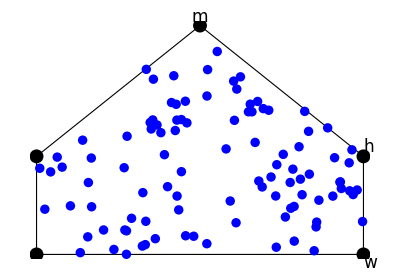

```mathematica
Module[{w,l,h,m,f,getdata,ll,ww,hh},
w=100;l=200;h=30;m=70;

f[x_]:=If[x<w/2,(m-h)/w *2* x+h,(m-h)/w*2*(w-x)+h];

getdata:=(
ww=RandomReal[w,{100}];
hh=RandomReal[f@#]&/@ww;
Transpose[{ww,hh}]);
Graphics[{
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,0},{w,0},{w,h},{w/2,m},{0,h}}]},
{PointSize@0.017,Blue,Point@getdata},
{PointSize@0.025,Point@{{0,0},{w,0},{w,h},{w/2,m},{0,h}}},
Text[Style[#1,17],#2,1.5*#3]&@@@{{"w",{w,0},{-1,1}},{"h",{w,h},{-1,-1}},{"m",{w/2,m},{0,-1}}}
}]
]
```